# (Top Project - dim6 ( Ctw,Cbw,CHud ,C3phiq ) and dim 8 ( C1quWH3 , C1qdWH3 , C2q2H4D , C3 q2H4D ,CudH4D ) - ALL Decay width - Chi^2 )

```mathematica
Quit[]
```

```mathematica
(* Activate FA/FC *)
$LoadFeynArts=True;
$FeynCalcStartupMessages=True;
<<FeynCalc`
$FAVerbose=0;
FAPatch[PatchModelsOnly->True];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

Successfully patched FeynArts.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll"];
```

Successfully patched FeynArts.

```mathematica
(* Load FR model *)
InitializeModel["/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"]
```

True

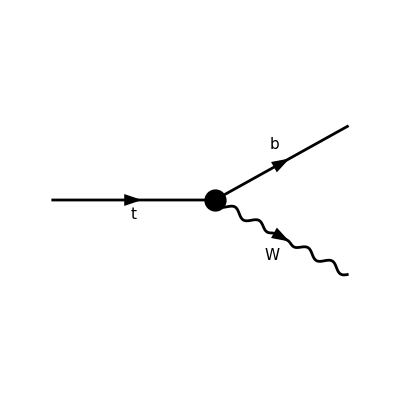

FeynArtsGraphics()(([] | Null | Null | Null | Null | Null))

```mathematica
(* Create diagrams *)
topo=CreateTopologies[0,1->2] (* # of loops = 0 *);

diag=InsertFields[topo,{F[9]}->{F[12], V[3]},InsertionLevel->{Particles},Model->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll",GenericModel->"/home/user1/Desktop/0000/FEYNCALC/Dim8New/LFullOperator6+8/LAll6and8twb/LFullOperatorAll/LFullOperatorAll"];
Paint[diag,ColumnsXRows->{6,1},Numbering->None,SheetHeader->False,ImageSize->{800,200}]
```

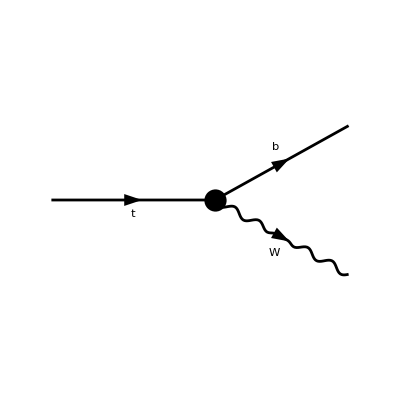

FeynArtsGraphics()(([]))

```mathematica
(* Diagram List *)
NofDiagrams=1;
lsD=Table[diag//DiagramDelete[#,Table[If[j≠i,j],{j,1,NofDiagrams}]/.Null->Sequence[]]&,{i,1,NofDiagrams}];
Paint[lsD[[1]],ColumnsXRows->{1,1},Numbering->None,SheetHeader->False,ImageSize->{200,100}]
```

```mathematica
(* Calculate amplitude *)
lsA0=Table[
FCFAConvert[CreateFeynAmp[lsD[[i]]],IncomingMomenta->{pt},OutgoingMomenta->{pb,pW},ChangeDimension->4,List->False,SMP->False,Contract->True,DropSumOver->True],
{i,1,NofDiagrams}];

lsA0=lsA0[[1]]//FeynAmpDenominatorExplicit//Simplify
(*%//TraditionalForm*)
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 gc139L Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^7+2 gc139R Lambda^4 (γ̄·(ε̄)^*(pW)).(γ̄)^6).(φ(OverBar[pt],FCGV(MT)))

```mathematica
gc139L =(FCGV["EL"]*(4*Lambda^4 + 2*C2q2H4D*vev^4 + C3q2H4D*vev^4 + 2*vev^4*Conjugate[C2q2H4D] + 4*Lambda^2*vev^2*Conjugate[C3phiq] - vev^4*Conjugate[C3q2H4D])*Conjugate[CKM3x3])/(4*Sqrt[2]*Lambda^4*sw);
     gc139R = (FCGV["EL"]*(Lambda^2*vev^2*Conjugate[CHud] + vev^4*Conjugate[CudH4D]))/(2*Sqrt[2]*Lambda^4*sw);
sw=e/g;
```

```mathematica
lsA0//FullSimplify
```

-ⅈ (φ(OverBar[pb],FCGV(MB))).1/(8 e Lambda^4)ⅈ δ_Col1Col2 (-4 e vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-4 e vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+2 √2 g Conjugate[CKM3x3] FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^7 (vev^4 (Conjugate[C2q2H4D]+C2q2H4D-Re(C3q2H4D)+C3q2H4D)+2 Lambda^2 vev^2 Conjugate[C3phiq]+2 Lambda^4)+2 √2 g vev^2 FCGV(EL) (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 Conjugate[CHud]+vev^2 Conjugate[CudH4D])).(φ(OverBar[pt],FCGV(MT)))

```mathematica
(* Simplify *)
(* Setup the kinematics *)
SetMandelstam[s,t,u,pt,pb,pW,mpt,mpb,mpW];

rep0={EL->e,CW->cW,SW->sW,MW->mW,ME->0,MB->mb,MT->mt,
Pair[Momentum[pt],Momentum[pt]]->mt^2,
Pair[Momentum[pb],Momentum[pb]]->mb^2,
Pair[Momentum[pW],Momentum[pW]]->mW^2};
lsA=(lsA0//ReplaceAll@{FCGV[x_String]:>ToExpression[x]}(*//DiracSimplify*))/.rep0
```

-ⅈ (φ(OverBar[pb],mb)).1/(2 Lambda^4)ⅈ δ_Col1Col2 (-vev ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^7-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^7) (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW])-vev Conjugate[CKM3x3] (C1quWH3 vev^2+2 CtW Lambda^2) ((γ̄·OverBar[pW]).(γ̄·(ε̄)^*(pW)).(γ̄)^6-(γ̄·(ε̄)^*(pW)).(γ̄·OverBar[pW]).(γ̄)^6)+(g Conjugate[CKM3x3] (γ̄·(ε̄)^*(pW)).(γ̄)^7 (2 vev^4 Conjugate[C2q2H4D]+2 C2q2H4D vev^4+4 Lambda^2 vev^2 Conjugate[C3phiq]-vev^4 Conjugate[C3q2H4D]+C3q2H4D vev^4+4 Lambda^4))/(2 √2)+(g (γ̄·(ε̄)^*(pW)).(γ̄)^6 (Lambda^2 vev^2 Conjugate[CHud]+vev^4 Conjugate[CudH4D]))/(√2)).(φ(OverBar[pt],mt))

```mathematica
Fspin[x_]:=x//SUNFDeltaContract//FermionSpinSum[#,ExtraFactor->1/2]&//ReplaceAll[#,DiracTrace->TR]&
(lsAsq=(lsA*ComplexConjugate[lsA])//Simplify//Fspin//Contract)
```

```mathematica
lsAsqq=lsAsq/.{SUNN->Nc}//FullSimplify
```

```mathematica
(* CALCULATION OF DECAY WIDTH and HELICITY FRACTION*)
```

```mathematica
Quit[]
```

```mathematica
g[c1_,c2_]:=a c1+b c2
```

```mathematica
X[c1_,c2_]:= g[c1,c2]-12
```

```mathematica
c1=0;
```

```mathematica
X[1,2]
```

-12+a+2 b

```mathematica
(*Compute decay width LEFT systematically*)
```

```mathematica
DecayWidthLeft[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1/(1024 Lambda^8 mt^5 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (8 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^6 Conjugate[C1qdWH3]^2+32 Lambda^4 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (-mb^2+mt^2+mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2))^2 vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CHud]^2+4 g^2 mt^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^8 Conjugate[CudH4D]^2+8 g Lambda^2 mt^2 vev^2 Conjugate[CHud] (g (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb Conjugate[CKM3x3] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 Lambda^2 mt (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CbW] (4 mb (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+8 (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mt^2 (mb^2-mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev Conjugate[CbW]+4 mb mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g mt (Lambda^2 (mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^2 Conjugate[CHud]+(mb^2+mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev^4 Conjugate[CudH4D]-2 mb mt Conjugate[CKM3x3] (2 Lambda^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mt^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (√2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(-((mb-mt+mw) (mb+mt+mw)))) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))+(mb^2+mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) Conjugate[CKM3x3]^2 (16 g^2 Lambda^8 mt^2+32 √2 CtW g Lambda^6 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev+16 √2 g Lambda^4 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])+32 Lambda^4 vev^2 (CtW^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq])+g^2 mt^2 vev^8 (4 C2q2H4D^2+C3q2H4D^2+4 C2q2H4D Conjugate[C2q2H4D]-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+8 (Conjugate[C2q2H4D]+2 ⅈ Im[C3q2H4D]) Re[C2q2H4D])+8 vev^6 (C1quWH3^2 (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 Conjugate[C3phiq] (C3q2H4D-Conjugate[C3q2H4D]+4 Re[C2q2H4D]))+16 √2 g Lambda^2 mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^2 vev^4 (2 C1quWH3 CtW (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2))^2+g^2 Lambda^2 mt^2 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+8 √2 C1quWH3 g mt (-mb^2+mt^2+mw^2+√(-((mb-mt-mw) (mb+mt-mw))) √(mt^2-(mb+mw)^2)) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))//FullSimplify
```

```mathematica
(*Compute decay width LONGITUDINAL systematically*)
```

```mathematica
DecayWidth0[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1/(1024 Lambda^8 mt^3 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (32 mw^4 (mb^2+mt^2-mw^2) vev^6 Conjugate[C1qdWH3]^2+128 Lambda^4 mw^4 (mb^2+mt^2-mw^2) vev^2 Conjugate[CbW]^2+4 g^2 Lambda^4 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^4 Conjugate[CHud]^2+4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[CudH4D]^2-8 g Lambda^2 vev^2 Conjugate[CHud] (g (-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) vev^4 Conjugate[CudH4D]+2 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+16 mw^2 vev^3 Conjugate[C1qdWH3] (8 Lambda^2 mw^2 (mb^2+mt^2-mw^2) vev Conjugate[CbW]-8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]-√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-32 Lambda^2 mw^2 vev Conjugate[CbW] (8 mb mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) Conjugate[CKM3x3]+√2 g (Lambda^2 mt (mb^2-mt^2+mw^2) vev^2 Conjugate[CHud]+mt (mb^2-mt^2+mw^2) vev^4 Conjugate[CudH4D]-mb (mb^2-mt^2-mw^2) Conjugate[CKM3x3] (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))-16 g mb mw^2 vev^4 Conjugate[CKM3x3] Conjugate[CudH4D] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D])))-Conjugate[CKM3x3]^2 (-16 g^2 Lambda^8 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2)+64 √2 CtW g Lambda^6 mt mw^2 (mb^2-mt^2+mw^2) vev-4 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^8 Conjugate[C2q2H4D]^2+32 √2 g Lambda^4 mt mw^2 (mb^2-mt^2+mw^2) vev^3 (C1quWH3+2 CtW Conjugate[C3phiq])-8 g^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) vev^6 Conjugate[C2q2H4D] (C2q2H4D vev^2+2 Lambda^2 Conjugate[C3phiq])-32 Lambda^4 vev^2 (4 CtW^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq])-16 vev^6 (2 C1quWH3^2 mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Conjugate[C3phiq] (C2q2H4D+C3q2H4D-Re[C3q2H4D]))+32 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^5 (C1quWH3 Conjugate[C3phiq]+CtW (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^2 vev^4 (8 C1quWH3 CtW mw^4 (mb^2+mt^2-mw^2)+g^2 Lambda^2 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]+Conjugate[C3phiq]^2-Re[C3q2H4D]))+16 √2 C1quWH3 g mt mw^2 (mb^2-mt^2+mw^2) vev^7 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])+g^2 vev^8 (-((4 C2q2H4D^2+3 C3q2H4D^2) (mb^2-mt^2)^2)+(4 C2q2H4D^2+C3q2H4D^2) (mb^2+mt^2) mw^2-2 C3q2H4D (mb^2+mt^2) mw^2 Conjugate[C3q2H4D]+(-(mb^2-mt^2)^2+(mb^2+mt^2) mw^2) Conjugate[C3q2H4D]^2-16 ((mb^2-mt^2)^2-(mb^2+mt^2) mw^2) Re[C2q2H4D] (C3q2H4D-Re[C3q2H4D])+4 C3q2H4D (mb^2-mt^2)^2 Re[C3q2H4D])))//FullSimplify
```

```mathematica
(*Compute decay width TOTAL systematically*)
```

```mathematica
DecayWidthTotal[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1/(4096 Lambda^8 mt^7 mw^2 π)√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2) Nc (16 g^2 Lambda^4 mt^4 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CHud]^2+16 mt^4 vev^2 (-8 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) vev^4 Conjugate[C1qdWH3]^2-32 Lambda^4 mw^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]^2-24 √2 g Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[CbW] Conjugate[CudH4D]+g^2 ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^6 Conjugate[CudH4D]^2-4 mw^2 vev^2 Conjugate[C1qdWH3] (8 Lambda^2 (-2 (mb^2-mt^2)^2+(mb^2+mt^2) mw^2+mw^4) Conjugate[CbW]+3 √2 g mt (mb^2-mt^2+mw^2) vev^3 Conjugate[CudH4D]))-32 g Lambda^2 mt^4 vev^2 Conjugate[CHud] (6 √2 mt mw^2 (mb^2-mt^2+mw^2) vev^3 Conjugate[C1qdWH3]+12 √2 Lambda^2 mt mw^2 (mb^2-mt^2+mw^2) vev Conjugate[CbW]-g ((mb^2-mt^2)^2+(mb^2+mt^2) mw^2-2 mw^4) vev^4 Conjugate[CudH4D]+6 mb mw^2 Conjugate[CKM3x3] (-√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)+g mt (2 Lambda^4+(C2q2H4D+C3q2H4D) vev^4)+g mt vev^2 (2 Lambda^2 Conjugate[C3phiq]+vev^2 (Conjugate[C2q2H4D]-Re[C3q2H4D]))))+48 mb mt (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) vev Conjugate[CKM3x3] (g mt vev^3 Conjugate[CudH4D] (√2 (mb^2-mt^2-mw^2) vev (2 CtW Lambda^2+C1quWH3 vev^2)-2 g Lambda^2 mt vev^2 Conjugate[C3phiq]-g mt (2 Lambda^4+C3q2H4D vev^4+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt (vev^2 Conjugate[C1qdWH3]+2 Lambda^2 Conjugate[CbW]) (8 mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2)-√2 g (mb^2-mt^2-mw^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))))+Conjugate[CKM3x3]^2 (4 mt^4 (mb^2-mt^2+mw^2) (-64 mw^2 (-mb^2+mt^2+mw^2) vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-48 √2 g mt mw^2 vev (2 CtW Lambda^2+C1quWH3 vev^2) (2 Lambda^4+C3q2H4D vev^4+2 Lambda^2 vev^2 Conjugate[C3phiq]+vev^4 (C2q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+g^2 (mb^2-mt^2-mw^2) (16 Lambda^8+(4 C2q2H4D^2+C3q2H4D^2) vev^8+8 C2q2H4D vev^8 Conjugate[C2q2H4D]+4 vev^8 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^4 Conjugate[C3phiq]^2+vev^8 (-2 C3q2H4D Conjugate[C3q2H4D]+Conjugate[C3q2H4D]^2+16 ⅈ Im[C3q2H4D] Re[C2q2H4D])+8 Lambda^2 vev^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))+16 Lambda^4 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D])))-mt^2 (mb^2+mt^2-mw^2) (mb^2-mt^2-mw^2-√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (mb^2-mt^2-mw^2+√((mb+mt-mw) (-mb+mt+mw)) √(mt^2-(mb+mw)^2)) (32 mw^2 vev^2 (2 CtW Lambda^2+C1quWH3 vev^2)^2-g^2 (16 Lambda^8+16 (C2q2H4D+C3q2H4D) Lambda^4 vev^4+(4 C2q2H4D^2+C3q2H4D^2) vev^8)-g^2 vev^2 (8 vev^2 (2 Lambda^4+C2q2H4D vev^4) Conjugate[C2q2H4D]+4 vev^6 Conjugate[C2q2H4D]^2+16 Lambda^4 vev^2 Conjugate[C3phiq]^2-2 C3q2H4D vev^6 Conjugate[C3q2H4D]+vev^6 Conjugate[C3q2H4D]^2+16 ⅈ vev^6 Im[C3q2H4D] Re[C2q2H4D]+8 Lambda^2 Conjugate[C3phiq] (4 Lambda^4+2 vev^4 (C2q2H4D+C3q2H4D+Conjugate[C2q2H4D]-Re[C3q2H4D]))-16 Lambda^4 vev^2 Re[C3q2H4D]))))//FullSimplify
```

```mathematica
FL[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=DecayWidthLeft[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]/DecayWidthTotal[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]//FullSimplify
```

```mathematica
F0[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=DecayWidth0[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]/DecayWidthTotal[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]//FullSimplify
```

```mathematica
FR[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=1-FL-F0//FullSimplify
```

```mathematica
(*Define parameters and constants based on PHYSICAL REVIEW D 100,056023 (2019)*)
Lambda=1000;e=0.31345;vev=246;g=0.6483;mb=4.78;mt=173.0; mw=80.379;CKM3x3=1;
FCGV["EL"]=e;Nc=1;
```

```mathematica
(* داده آزمایش-FLexp = 0.320 +- 0.013 *)
FLexp=0.320;
F0exp=0.687;
DecayWidthTotalexp=1.41;
```

```mathematica
(* Maximum Value of CHud=12.84;CtW=0.17;CbW=2.07;;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud;
CtW=0;
CbW=0;
C3phiq=0;
C1quWH3=0;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D;
CudH4D=0;
```

```mathematica
rho={{1.0,0.0,0.0},{0.0,1.0,-0.87},{0.0,-0.87,1.0}};
sigma={0.19,0.018,0.013};
```

```mathematica
Sigma = Table[sigma[[i]] * rho[[i, j]] * sigma[[j]], {i, 3}, {j, 3}];
SigmaInv = Inverse[Sigma]
```

{{27.7008,0.,0.},{0.,12696.1,15293.9},{0.,15293.9,24340.4}}

```mathematica
Fth[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:={DecayWidthTotal[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],F0[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],FL[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]};  

Fexp={DecayWidthTotalexp,F0exp,FLexp};     

Chi2[CtW_,CbW_,C3phiq_,CHud_,C1quWH3_,C1qdWH3_,C2q2H4D_,C3q2H4D_,CudH4D_]:=Module[{delta},delta=Fth[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]-Fexp; delta.SigmaInv.delta]
```

```mathematica
(* check for working*)
```

```mathematica
(*Fth[CtW,0,0,0,C1quWH3,0,0,0,0]*)
```

```mathematica
(*Module[{delta},delta=Fth[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]-Fexp; delta.SigmaInv.delta]*)
```

```mathematica
Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]
```

(0.+27.7008 (0.0607269+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D])) (0.0607269+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D])+(-0.687+(1.02626+(0.00375835+2.58071×10^-6 C3q2H4D) C3q2H4D+8.60237×10^-7 Conjugate[C3q2H4D]^2+0.000939588 Conjugate[CHud]^2+Conjugate[CHud] (-0.000946851-1.73377×10^-6 C3q2H4D+1.73377×10^-6 Re[C3q2H4D])+(-0.00375835-3.44095×10^-6 C3q2H4D) Re[C3q2H4D])/(1.47073+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D])) (0.+15293.9 (-0.32+(0.443916+(0.0016257+3.72102×10^-7 C3q2H4D) C3q2H4D-7.44204×10^-7 C3q2H4D Conjugate[C3q2H4D]+3.72102×10^-7 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.000946851-1.73377×10^-6 C3q2H4D+5.04897×10^-7 Conjugate[CHud]+1.73377×10^-6 Re[C3q2H4D])-0.0016257 Re[C3q2H4D])/(1.47073+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D]))+12696.1 (-0.687+(1.02626+(0.00375835+2.58071×10^-6 C3q2H4D) C3q2H4D+8.60237×10^-7 Conjugate[C3q2H4D]^2+0.000939588 Conjugate[CHud]^2+Conjugate[CHud] (-0.000946851-1.73377×10^-6 C3q2H4D+1.73377×10^-6 Re[C3q2H4D])+(-0.00375835-3.44095×10^-6 C3q2H4D) Re[C3q2H4D])/(1.47073+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D])))+(-0.32+(0.443916+(0.0016257+3.72102×10^-7 C3q2H4D) C3q2H4D-7.44204×10^-7 C3q2H4D Conjugate[C3q2H4D]+3.72102×10^-7 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.000946851-1.73377×10^-6 C3q2H4D+5.04897×10^-7 Conjugate[CHud]+1.73377×10^-6 Re[C3q2H4D])-0.0016257 Re[C3q2H4D])/(1.47073+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D])) (0.+24340.4 (-0.32+(0.443916+(0.0016257+3.72102×10^-7 C3q2H4D) C3q2H4D-7.44204×10^-7 C3q2H4D Conjugate[C3q2H4D]+3.72102×10^-7 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.000946851-1.73377×10^-6 C3q2H4D+5.04897×10^-7 Conjugate[CHud]+1.73377×10^-6 Re[C3q2H4D])-0.0016257 Re[C3q2H4D])/(1.47073+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D]))+15293.9 (-0.687+(1.02626+(0.00375835+2.58071×10^-6 C3q2H4D) C3q2H4D+8.60237×10^-7 Conjugate[C3q2H4D]^2+0.000939588 Conjugate[CHud]^2+Conjugate[CHud] (-0.000946851-1.73377×10^-6 C3q2H4D+1.73377×10^-6 Re[C3q2H4D])+(-0.00375835-3.44095×10^-6 C3q2H4D) Re[C3q2H4D])/(1.47073+(0.00538608+1.2328×10^-6 C3q2H4D) C3q2H4D-2.4656×10^-6 C3q2H4D Conjugate[C3q2H4D]+1.2328×10^-6 Conjugate[C3q2H4D]^2+Conjugate[CHud] (-0.00284055-5.20132×10^-6 C3q2H4D+0.00134652 Conjugate[CHud]+5.20132×10^-6 Re[C3q2H4D])-0.00538608 Re[C3q2H4D])))

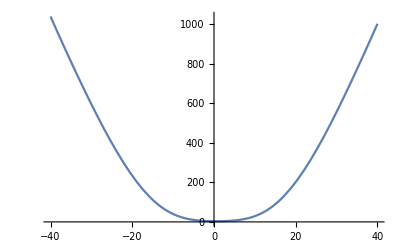

```mathematica
Plot[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,0,CudH4D],{CHud,-40,40}]
```

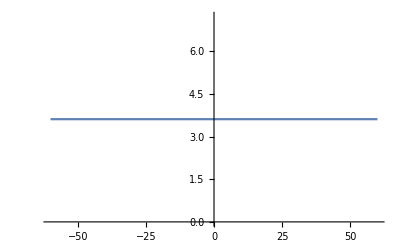

```mathematica
Plot[Chi2[CtW,CbW,C3phiq,0,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C3q2H4D,-60,60}]
```

```mathematica
Minimize[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C3q2H4D,CHud}]
```

{3.56945,{C3q2H4D→0.715333,CHud→0.545633}}

```mathematica
bestFit=Last@Minimize[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C3q2H4D,CHud}]
```

{C3q2H4D→0.715333,CHud→0.545633}

```mathematica
chi2min=First@Minimize[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D],{C3q2H4D,CHud}]
```

3.56945

```mathematica
shiftedChi2[c1_,ct_]:=Chi2[c1+bestFit[[1,2]],ct+bestFit[[2,2]]]
```

```mathematica
shiftedChi2[C3q2H4D,CHud]
```

Chi2[0.715333+C3q2H4D,0.545633+CHud]

```mathematica
chi2min=3.56945;
deltaChi2=3.2;  (*for 68% CL with 2 parameters*)
deltaChi22=5.99;  (*for 95% CL with 2 parameters*)
```

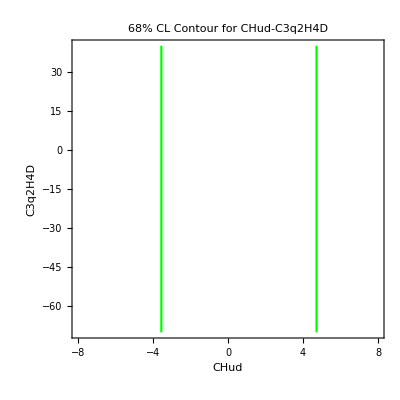

```mathematica
ContourPlot[Evaluate[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]==chi2min+deltaChi2],{CHud,-8,8},{C3q2H4D,-70,40},AspectRatio->1,PlotPoints->100,FrameLabel->{"CHud","C3q2H4D"},PlotLabel->"68% CL Contour for CHud-C3q2H4D",ContourStyle->Green]
```

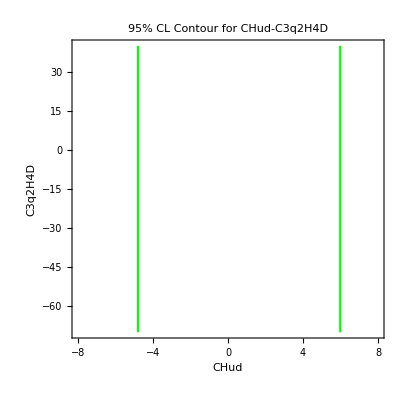

```mathematica
ContourPlot[Evaluate[Chi2[CtW,CbW,C3phiq,CHud,C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D]==chi2min+deltaChi22],{CHud,-8,8},{C3q2H4D,-70,40},AspectRatio->1,PlotPoints->100,FrameLabel->{"CHud","C3q2H4D"},PlotLabel->"95% CL Contour for CHud-C3q2H4D",ContourStyle->Green]
```

```mathematica
(* Minimum Value of CHud=12.84;CtW=-0.05;CbW=2.07;C3phiq=0*)
```

```mathematica
Clear[C1quWH3,C1qdWH3,C2q2H4D,C3q2H4D,CudH4D,CHud,C3phiq,CtW,CbW]
```

```mathematica
CHud=-4.15;
CtW=-0.05;
CbW=-0.47;
C3phiq=0;
C1quWH3;
C1qdWH3=0;
C2q2H4D=0;
C3q2H4D=0;
CudH4D=0;
```